2

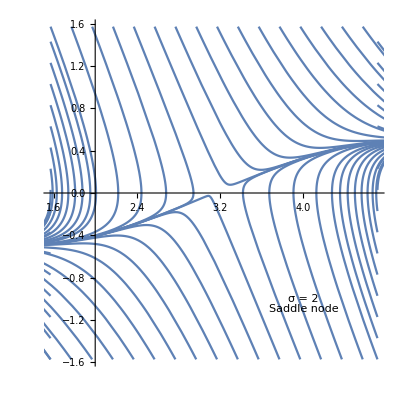

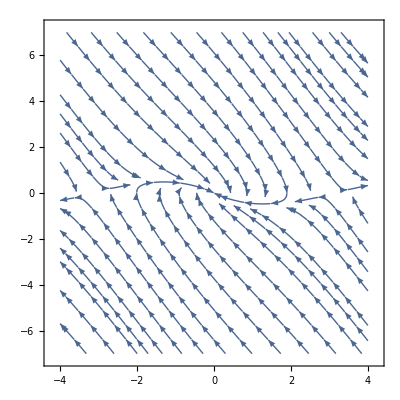

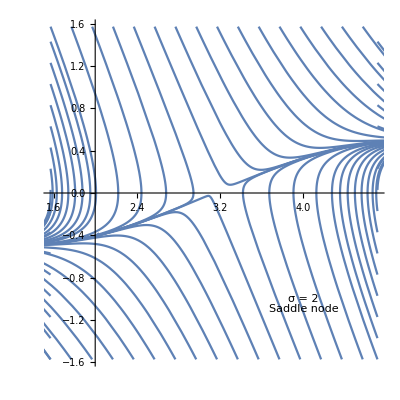

```mathematica
si = 2
s=NDSolve[{x'[t]==y[t],y'[t]==-Sin[x[t]]-si*y[t],x[0]==y[0]==0},{x[t],y[t]},{t,0,10}];
minx=Pi/2;
miny=-Pi/2;
maxx=3*Pi/2;
maxy=Pi/2;
dist=0.2;
sol[x0_,y0_]:=NDSolve[{x'[t]==y[t],y'[t]==-Sin[x[t]]-si*y[t],x[0]==x0,y[0]==y0},{x,y},{t,10}];
inits=Join[Table[{minx,y},{y,miny,maxy,dist}],Table[{maxx,y},{y,miny,maxy,dist}],Table[{x,miny},{x,minx,maxx,dist}],Table[{x,maxy},{x,minx,maxx,dist}]];
text = Graphics[Text["σ = 2", {4,-1}]];
text2 = Graphics[Text["Saddle node", {4, -1.1
}]];
p0 =Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[inits[[i,1]],inits[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[inits]}], text, text2]
StreamPlot[{y,-Sin[x]-si*y},{x,-4,4},{y,-7,7}]

(p0//Normal)/.Line[x_]:>{Arrowheads[{0.05,0.05,0.05}],Arrow[x]}
```

```mathematica
1sol
```

sol

```mathematica
sol[x0,y0]
```

```mathematica
streamplot=Show[
StreamPlot[flow,{x,-2,2},{y,-2,2}],
Graphics[{PointSize[Large],Red,Point[{x,y}/.fixsol]}]
]
```

```mathematica
M = {{0, 1},{-1, -sigma}}
```

{{0,1},{-1,-sigma}}

```mathematica
M//MatrixForm
```

(0 | 1
-1 | -sigma)

```mathematica
Eigenvalues[M]
```

{1/2 (-sigma-√(-4+sigma^2)),1/2 (-sigma+√(-4+sigma^2))}

{{sigma→2 (-1-√2)},{sigma→2 (-1+√2)}}